# QMRITools Demonstration

In this demo notebook some functionality of the QMRI toolbox is demonstrated.
Not all functionality is covered, some functions are very specialized for experiments only run in our lab. 
Furthermore some functionality is still under development and therefore will also be excluded from the demos.
If you need any extra information about one of the function please feel free to contact me at m.froeling@gmail.com

## Initialization

### Loading the toolbox definitions

Load the toolbox and specify the directory of the demo data folder. It assumes the demo data folder is in the same folder as the demo.nb

```mathematica
<<QMRITools`
ExtractDemoData[];
SetDirectory[FileNameJoin[{DirectoryName[GetAssetLocation["DemoData"]],"DemoData"}]];
PacletFind["QMRITools"]
```

See the location of the installation directory

```mathematica
SystemOpen[First[PacletFind["QMRITools"]]["Location"]]
```

### Verbose loading

If the private parameter verbose is set to True the initialization of the toolbox is done printing all the steps done by the init.m file.

```mathematica
QMRITools`$Verbose=True;
<<QMRITools`
QMRITools`$Verbose=False;
```

### List all Packages and toolboxes

List of all the QMRITool packages and functions that are loaded. For more information about the functions open the “All-Functions.nb”

```mathematica
QMRIToolsPackages[]
```

```mathematica
QMRIToolsFunctions[4]
```

```mathematica
CompilableFunctions[]
```

```mathematica
NotebookOpen@FileNameJoin[{First[PacletFind["QMRITools"]]["Location"],"Resources","All-Functions.nb"}];
```

### Memory Usage

MemoryUsage gives a visual overview of all datasets in memory.

```mathematica
MemoryUsage[]
```

Imaging datasets can become large so it can be good to clear them from memory if needed.

### List of Resources

```mathematica
TableForm[{#,GetAssetLocation[#]}&/@{"Elastix","Transformix","DcmToNii","pigz","Demo","DemoData","GradientTool","ColorData"}]
```

### Visualize Function Dependance

#### All functions

```mathematica
(*load all functions and contexts*)
{tool,funcs}=Transpose[QMRIToolsFunctions[][[All,1;;2]]];

(*list most complicated functions*)
Grid[Quiet[Reverse[Sort[{VertexCount[MakeFunctionGraph[#]],#}&/@Flatten[funcs]]][[1;;15]]][[All,{2,1}]]]

(*visualize each function*)
Manipulate[
p=First@First@Position[tool,tl];
If[f==="",Graphics[],Column[{Style[f, Black,Large,Bold],
MakeFunctionGraph[f,LabelPlacement->name,AllowSelfDependencies->dep]
},Alignment->Center]],
{{tl,First@tool,"ToolBox"},tool},
{{f,"","Function"},Dynamic[funcs[[p]]],ControlType->PopupMenu},
{{name,Tooltip,"Show Name"},{Tooltip,Automatic}},
{{dep,False,"Self Ref"},{True,False}},
Initialization:>{p=1,f=""},SaveDefinitions->True
]
```

#### MuscleBidsProcess

```mathematica
nAll = Length@DeleteDuplicates[Flatten[VertexList[Quiet@MakeFunctionGraph[#]]&/@Flatten[funcs[[1;;]]]]];
gr=MakeFunctionGraph[MuscleBidsProcess];
nPro=ToString@VertexCount@gr;

Column[{
Style["Number public and private QMITools functions: "<>ToString@nAll,Black,Bold,16],
Style["Number of functions used in MuscleBidsProcess: "<>ToString@nPro,Black,Bold,16],
"",Graph[gr,VertexSize->Automatic,ImageSize->800]
},Alignment->Center]
```

## Basic Data manipulation and visualisation

### Importing Data

QMRITools mostly uses the nii file format for importing and exporting data. ImportNii imports the data and the voxel size.

```mathematica
{data,vox}=ImportNii["twoLegs.nii"];
```

With NiiMethod other hdr elements can be imported

```mathematica
{data,vox,hdr}=ImportNii["twoLegs.nii",NiiMethod->"header"];
hdr//Column
```

```mathematica
{data,vox,rot}=ImportNii["twoLegs.nii",NiiMethod->"rotation"];
rot
```

To convert Dcm to nii format used DcmToNii

```mathematica
DcmToNii[]
```

All Nii files in a folders can be compressed or uncompressed using "CompressNiiFiles" and "ExtractNiiFiles".
The nii import function is blind to the .gz extension.

```mathematica
CompressNiiFiles[]
```

```mathematica
ExtractNiiFiles[]
```

### Plotting data Data

QMRITools contains various function for displaying multi dimensional data .

```mathematica
(*plot the data*)
PlotData[data,vox]
```

```mathematica
(*plot the data in 3D viewer*)
PlotData3D[data,vox]
```

```mathematica
(*plot the data with predefined range and color function*)
PlotData[data,vox,PlotRange->{10,90},ColorFunction->"Rainbow"]
```

```mathematica
(*plot two data sets*)
PlotData[data, AddNoise[data,5],vox]
```

Using GridData a mosaic of the slices can be generated, to minimize background AutoCropData can be used.

```mathematica
(*plot the data as a grid*)
PlotData[GridData[data,5]]
```

```mathematica
(*plot every third slice of the the data as a grid*)
PlotData[GridData[data[[;;;;3]],3]]
```

```mathematica
(*plot every third slice of the the data as a grid, with auto cropping*)
PlotData[GridData[First[AutoCropData[data]][[1;;;;3]],3]]
```

```mathematica
(*3D data viewer, Still work in progress*)
PlotData3D[AutoCropData[data][[1]],vox]
```

### Automatically find cross section images

GetSlicsPosition automatically finds the slices with the highest signal intensity in all three orientations
By also providing the voxel size the pos is in mm else it will be in voxel position.

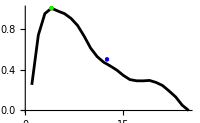
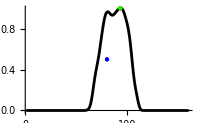
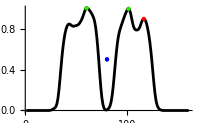

-Graphics--Graphics--Graphics-

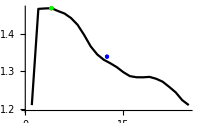
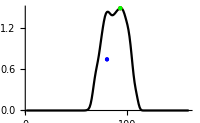
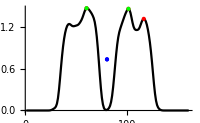

-Graphics--Graphics--Graphics-

```mathematica
(*get the positions and the data on those positions*)
pos=GetSlicePositions[data,MakeCheckPlot->True];
pdat=GetSliceData[data,pos];
```

```mathematica
(*make images of the data*)
Grid[MakeSliceImages[pdat,vox,ColorFunction->"DarkRainbow",ImageLegend->True]]
```

### Rescaling Data

Datasets can be rescaled to different resolutions.

```mathematica
(*to specific dimensions*)
dataReD=RescaleData[data,{50,100,100}];

Dimensions[data]
Dimensions[dataReD]
```

```mathematica
(*to specific voxel Size*)
voxNew={4,2,2};
dataRe=RescaleData[data,{vox,voxNew}];

Dimensions[data]
Dimensions[dataRe]
```

### Data Operations

#### Rotate data Dimensions

Rotate the dimensions left or right

```mathematica
Dimensions/@{data,RotateDimensionsLeft@data,RotateDimensionsRight@data,RotateDimensionsLeft[data,2],ReverseDimensions@data}
```

#### Remove singleton dimensions from data

```mathematica
dataS={{#}&/@data};
Dimensions@dataS
Dimensions@Squeeze@dataS
```

#### Data array to vector

Convert non zero values to data vector

```mathematica
{vec,{dim, coor}}=DataToVector[data];
Dimensions/@{data,vec}
```

Convert vector back to array

```mathematica
data2=VectorToData[vec,{dim,coor}];
data===data2
```

### Cropping

#### Automatic crop

To automatically remove the background from images FindCrop or AutoCropData can be used .

```mathematica
(*Find corp finds the crop values to remove zero background*)
crop=FindCrop[data]
```

```mathematica
(*apply thecropping*)
dataCrop=ApplyCrop[data,crop];
```

```mathematica
PlotData[dataCrop,vox]
```

```mathematica
(*do this in one go*)
{dataCrop,crop}=AutoCropData[data];
```

```mathematica
PlotData[dataCrop,vox]
```

#### Apply To Rescaled Data

When the crop dimensions were defined on a dataset with different voxel size this can still be used .

```mathematica
dataCR=ApplyCrop[dataRe,crop,{vox,voxNew}];
```

```mathematica
PlotData[dataCR]
```

#### Reverse the Crop

When the data was cropped the original dimensions can be restored.

```mathematica
(*reverse the crop to the original dimensions*)
dim=Dimensions[data]
dataRev=ReverseCrop[dataCrop,dim,crop];
Dimensions[dataRev]
dataRev==data
```

#### Manual crop

```mathematica
(*manually find the crop dimensions with a interactive viewer*)
{dataCropM,crop}=CropData[data,vox];
Dimensions[dataCropM]
```

```mathematica
PlotData[dataCropM,vox]
```

### Splitting Data

#### Split and Stitch

Often muscle data is scanned bilaterally however it is better to analyze both legs separately.

```mathematica
(*automatically split the data into left and right*)
{left,right,cut}=CutData[data,True];
cut
```

```mathematica
PlotData[left,right,vox]
```

```mathematica
(*join the data back together*)
dataStich=StichData[left,right];
data==dataStich
```

```mathematica
PlotData[dataStich]
```

```mathematica
(*cut with known value*)
{left,right,cut}=CutData[data,80];
```

#### Example make both legs left

```mathematica
(*Split in Left and right leg*)
{left,right,cut}=CutData[data];
(*crop to minimal Space and flip right leg*)
{leftC,rightC}=AutoCropData[#][[1]]&/@{left,right};
rightC=Reverse[rightC,{3}];
dataC={leftC,rightC};
(*find maximal common dimensions and make into one dataset of same dimensions*)
dimMax=FindMaxDimensions[dataC];
dataP=Transpose[PadToDimensions[#,dimMax]&/@dataC];
```

```mathematica
PlotData[dataP,vox]
```

### Joining multiple stacks

#### Import

Data can be acquired in multiple stacks  as in the example below

```mathematica
{dataJ,voxJ}=Transpose[ImportNii/@FileNames["Join*.nii.gz",""]];
overlap=5;(*number of slice overlap between stacks*)
```

```mathematica
all=Flatten[ArrayPad[#,{{2,2},{0,0},{0,0}}]&/@dataJ,1];
MakeSliceImages[GetSliceData[all,{{},{140},{}}],voxJ[[1]]][[2,1]]
```

With JoinSets multiple stacks which have overlapping slices can be joined into one set. 
If There is motion between the stacks this can be resolved using the option MotionCorrectSets which uses rigid registration of the overlap to align the sets.
Using JoinSetSplit the data can be split into a left and right side.

```mathematica
Column@Options@JoinSets
```

#### Joining multiple data sets

```mathematica
(*joining the sets with data normalization*)
joined=JoinSets[dataJ,overlap,ReverseSets->True];
Row[Flatten@{MakeSliceImages[GetSliceData[all,{{},{140},{}}],voxJ[[1]]],MakeSliceImages[GetSliceData[joined,{{},{140},{}}],voxJ[[1]]]}]
```

```mathematica
(*joining the sets with data normalization and motion correction*)
joinedC=JoinSets[dataJ,overlap, ReverseSets->True, MotionCorrectSets->True,NormalizeSets->False];
```

```mathematica
Row[Flatten@{MakeSliceImages[GetSliceData[all,{{},{140},{}}],voxJ[[1]]],MakeSliceImages[GetSliceData[joined,{{},{140},{}}],voxJ[[1]]],MakeSliceImages[GetSliceData[joinedC,{{},{140},{}}],voxJ[[1]]]}]
```

```mathematica
PlotData[NormalizeData@joined,NormalizeData@joinedC,voxJ[[1]]]
```

Using MotionCorrectSets->True is similar to using CorrectjoinSetMotion

```mathematica
joinedC2=JoinSets[CorrectJoinSetMotion[dataJ,voxJ[[1]],overlap],overlap];
```

```mathematica
(*display the data with PlotData*)
vis1=Flatten[ArrayPad[#,{1,0,0},-10]&/@dataJ,1];
vis2=ArrayPad[joined,{22,0,0}];
PlotData[vis1,vis2,voxJ[[1]],PlotRange->{0,500}]
```

#### Splitting joined data

After joining datasets they can also be split back into separate stacks

```mathematica
split=SplitSets[joined,7,5];
Dimensions/@{dataJ,joined,split}
```

## General functions

### Define Data

Noise1 contains no zero values with mean 50 and standard deviation 10, noise 2 has 10 zero columns

```mathematica
noise1=RandomVariate[NormalDistribution[50,10],{50,60,70}];
noise2=RandomVariate[NormalDistribution[50,10],{50,60,70}];
noise2[[All,1;;10]]=0noise2[[All,1;;10]];
```

```mathematica
PlotData[noise1,noise2]
```

### Filters

Laplacian Filtering

```mathematica
fil1=LapFilter[noise2,1];
PlotData[noise2,fil1,PlotRange->{30,70}]
```

Find the local StandardDeviation

```mathematica
fil2=StdFilter[noise2,5];
PlotData[noise2,fil2,PlotRange->{{30,70},{5,15}}]
```

### Operation ignoring zeros

Calculate statistics while ignoring zero values

```mathematica
{MeanNoZero@Flatten@noise2,Mean@Flatten@noise2}
```

```mathematica
{MedianNoZero@Flatten@noise2,Median@Flatten@noise2}
```

```mathematica
{MADNoZero@Flatten@noise2,MedianDeviation@Flatten@noise2}
```

```mathematica
{RMSNoZero@Flatten@noise2,RootMeanSquare@Flatten@noise2}
```

Mathematical operators ignoring zero values and keeping them zero.

```mathematica
Grid@{
{Exp[0.],ExpNoZero[0.]},
{Log[0.],LogNoZero[0.]},
{1/0.,DevideNoZero[1,0]}
}
```

```mathematica
Quiet@AllTrue[noise1/noise2,NumericQ,3]
AllTrue[DevideNoZero[noise1,noise2],NumericQ,3]
```

```mathematica
noised=DevideNoZero[noise1,noise2];
PlotData[noised]
```

## Masking

### Import Data

```mathematica
(*simple 3D dataset with segmentations*)
{data,vox}=ImportNii["twoLegs.nii"];
{labels,vox}=ImportNii["labels.nii"];
```

### Create Mask

#### Automated and threshold masking

Automated Binarization.
Normalize the data to the mean of the data such that the mean data within an automated mask will be 100.

```mathematica
dataN=NormalizeData[data];
mask=Mask[dataN,MaskDilation->1];
dataH=HomogenizeData[dataN];

{MeanNoZero@GetMaskData[data,mask],MeanNoZero@GetMaskData[dataN,mask],MeanNoZero@GetMaskData[dataH,mask]}
```

```mathematica
PlotData[dataN,dataH]
```

```mathematica
PlotData[data,dataN]
```

```mathematica
PlotData[data,mask]
```

Various ways of defining manual mask thresholds

```mathematica
masks={Mask[dataN],Mask[dataN,10],Mask[dataN,{15,60}]};
PlotData[GridData[masks,3]]
```

Automatic generation of mask based on several datasets

```mathematica
maskC=Mask[{{data,15},{dataN,15},{dataN,{15,80}}}];
PlotData[maskC]
```

#### Mask smoothing

Clean up the mask. By default it will only find one mask component, but you can force the method to find more components.

```mathematica
cleanMask1=SmoothMask[mask];
```

```mathematica
cleanMask2=SmoothMask[mask,MaskComponents->2];
```

```mathematica
Row[PlotContour[AutoCropData[#][[1]],vox]&/@{mask,cleanMask1,cleanMask2}]
```

```mathematica
PlotData[data,Transpose@{cleanMask1,cleanMask2},vox]
```

Create mask based on threshold, smooth the mask, close holes larger then two, maintain two separate masks.
Default the algorithm finds only one mask but it is possible to maintain two separate masks.

```mathematica
cleanMask1=Mask[data,15,MaskSmoothing->True,MaskClosing->2,MaskComponents->1];
```

```mathematica
cleanMask2=Mask[data,15,MaskSmoothing->True,MaskClosing->2,MaskComponents->2];
```

```mathematica
PlotData[data,Transpose@{cleanMask1,cleanMask2},vox]
```

Apply the mask

```mathematica
dataMask=MaskData[data,cleanMask2];
```

```mathematica
PlotData[data,dataMask]
```

#### Manual segmentation processing

Separate a segmentation with multiple labels into individual masks.

```mathematica
{seg,lab}=SplitSegmentations[labels];
crp=FindCrop[labels];
lab (*the label numbers*)
Dimensions[labels]
Dimensions[seg]
```

```mathematica
PlotData[labels,seg]
```

Smooth the segmentations labels should be separate volumes and can be joined after smoothing

```mathematica
labelsS=SmoothSegmentation[labels];
```

```mathematica
{PlotContour[SplitSegmentations[AutoCropData[labels][[1]]][[1]],vox,ContourColor->"Random"],
PlotContour[SplitSegmentations[AutoCropData[labelsS][[1]]][[1]],vox,ContourColor->"Random"]}
```

```mathematica
PlotData[labels,labelsS,vox]
```

If segmentations have overlaps they can be removed.

```mathematica
segDil=Transpose[SparseArray@Dilation[Normal@#,1]&/@Transpose[seg]];
```

```mathematica
labelsD=MergeSegmentations[segDil,lab];
labelsDCor=MergeSegmentations[RemoveMaskOverlaps[segDil],lab];
```

```mathematica
PlotData[labelsD,labelsDCor]
```

#### Splitting segmentation in slice direction

Split a Segmentation in 5 equal parts along the slice direction

```mathematica
segSplit=SegmentMask[seg[[All,5]],5];
Dimensions[segSplit]
```

```mathematica
segPlot=MergeSegmentations[Transpose@segSplit,{1,2,3,4,5}];
Row@Flatten@MakeSliceImages[GetSliceData[segPlot,{{},{90},{57}}],vox,ColorFunction->"DarkRainbow",ImageLegend->True]
```

#### Extract Data from Masks

Use masks to get mean value from data

```mathematica
segData=GetMaskData[data,#]&/@Transpose[seg];
```

```mathematica
MeanStd/@segData
```

```mathematica
MeanRange/@segData
```

```mathematica
TableForm@GetMaskMeans[data,seg,"lab"]
```

### Rescaling Segmentations

```mathematica
Dimensions[labels]
labelsRescale=RescaleSegmentation[labels,{50,100,100}];
Dimensions[labelsRescale]
```

```mathematica
mask=Mask[data,MaskSmoothing->True,MaskComponents->2];
Dimensions[mask]
maskRescale=RescaleSegmentation[mask,{50,100,100}];
Dimensions[maskRescale]
```

```mathematica
PlotData[labelsRescale,RescaleData[labels,{50,100,100}]]
```

## Automatic segmentation

### UNET Neural Network

#### Make Network

Automated segmentation is based on a UNET neural network . The included segmentation functions are all based on this network.
A UNET can be generated and manipulated with a number of functions.
To generate a UNET the number of input channels, output classes and the input patch size need to be given .
Other settings can be controlled with options .

```mathematica
Column@Options@MakeUnet
```

```mathematica
net=MakeUnet[2,4,{16,80,80}]
```

Get information from the network

```mathematica
PrintKernels[net]
```

#### Configure all aspects of the network

```mathematica
nChan=1;
nClass=12;
netPar=32;
depth=5;
shed={{1,2,2},{2,2,2} ,{1,2,2},{2,2,2}};
patch={32,112,112};
dropout= 0.1;
block="ResNet";

netU=MakeUnet[nChan,nClass,patch, 
InputFilters->netPar,
BlockType->block,
NetworkDepth->depth,
DropoutRate->dropout,
DownsampleSchedule->shed
]
```

#### Change the network

Some features of a network can be changed without affecting the trained elements, others need retraining.
For the retraining only the start and mapping layer need to be retrained.

```mathematica
netI=NetInitialize[netU];
```

```mathematica
NetDimensions[netI]
```

```mathematica
netI1=ChangeNetDimensions[netI,"Dimensions"->{48,112,112}]
NetDimensions[netI1]
```

```mathematica
netI2=ChangeNetDimensions[netI,"Channels"->3,"Classes"->17,"Dimensions"->{48,112,112}]
NetDimensions[netI2]
```

#### Add Loss Layer

To train a network a loss function needs to be defined and added .

```mathematica
lossNet=AddLossLayer[netU]
```

### Data manipulation

#### Import Data

```mathematica
{segData,segV}=ImportNii["seg_data.nii"];
{segLab,segV}=ImportNii["seg_label.nii"];
nClass=Round@Max@segLab;
```

```mathematica
PlotData[segData,segLab,segV]
```

#### Make patches

By default all possible patches that need to be made to fully cover the data are generated with minimal overlap of the patches.
It also provides the coordinates of the patch within the original dataset.

```mathematica
patch={64,128,128};
{patches,loc}=DataToPatches[segData,patch];
{Dimensions@segData,Dimensions@patches}
Column@loc
```

```mathematica
PlotData[GridData[patches,3]]
```

Combine the patches to recreate the original dataset .

```mathematica
segDataRec=PatchesToData[patches,loc];
segData==segDataRec
```

### Data Augmentation

#### Dynamic visualization of augmentation function

```mathematica
dynVox=2 segV;
dynDat=RescaleData[segData,{ segV,dynVox}];
dynSeg=RescaleSegmentation[segLab,{ segV,dynVox}];
rr=MinMax[dynSeg];
dynD=Dimensions[dynDat];

{z,x,y}=Round[dynD/2];
scale={f1,f2,f3}= dynD dynVox;
Manipulate[

{time,{datT,segT}}=AbsoluteTiming[{
DataTransformation[dynDat,dynVox,{r1,r2,r3, t1, t2,t3,s1,s2,s3,0,0,0},InterpolationOrder->1],
DataTransformation[dynSeg,dynVox,{r1,r2,r3, t1, t2,t3,s1,s2,s3,0,0,0},InterpolationOrder->0]
}];

Grid[{{time,SpanFromLeft,SpanFromLeft},
{
Show[MakeChannelClassImage[{datT[[z,All,All]]},segT[[z,All,All]],rr],AspectRatio->Divide@@scale[[{2,3}]],ImageSize->{Automatic,300}],
Show[MakeChannelClassImage[{Reverse@datT[[All,x,All]]},Reverse@segT[[All,x,All]],rr],AspectRatio->Divide@@scale[[{1,3}]],ImageSize->{Automatic,300}],
Show[MakeChannelClassImage[{Reverse@datT[[All,All,y]]},Reverse@segT[[All,All,y]],rr],AspectRatio->Divide@@scale[[{1,2}]],ImageSize->{Automatic,300}]
}}]

,{{r1,0},-90,90,1}
,{{r2,0},-90,90,1}
,{{r3,0},-90,90,1}

,{{s1,1},0.5,1.5}
,{{s2,1},0.5,1.5}
,{{s3,1},0.5,1.5}

,{{t1,0},-f1 0.1,f1 0.1}
,{{t2,0},-f2 0.4,f2 0.4}
,{{t3,0},-f3 0.4,f3 0.4}

,ControlPlacement->Left
]
```

#### Data Augmentation

Generate an augmented version of the dataset

```mathematica
{augData,augLab}=AugmentTrainingData[{segData,segLab},segV];
```

```mathematica
PlotData[Transpose@{segData,augData},Transpose@{segLab,augLab},segV]
```

Generate 20 patches with augmentation of the same dataset, using reduces dimensions for demonstration purposes

```mathematica
test=Table[AugmentTrainingData[{dynDat,dynSeg},dynVox,{True,True,True,True,True,True,False}],{i,20}];//AbsoluteTiming
PlotData[Transpose@test[[All,1]],Transpose@test[[All,2]],dynVox]
```

### Get Training Data

#### Visualize Train data

Visualize the channel data

```mathematica
MakeChannelImage[{segData}]
MakeClassImage[segLab,segV]
MakeChannelClassImage[{segData},segLab,{0,nClass},segV]
```

#### Augment train data

For training the loading and augmentation can be combined, this can be done from disk or from memory.
The set one augmentation step is done, then one or multiple patches can be created from the same set

```mathematica
trainDat=GetTrainData[{{"seg_data.nii","seg_label.nii"}},9,patch,PatchesPerSet->1];
```

```mathematica
trainDat=GetTrainData[{{segData,segLab,segV}},9,patch,PatchesPerSet->1];//AbsoluteTiming
Grid@Partition[MakeChannelClassImage[#[[1]],#[[2]],{1,nClass}, segV]&/@trainDat,3]
```

```mathematica
trainDat1=GetTrainData[{{segData,segLab,segV}},6,patch,PatchesPerSet->1];//AbsoluteTiming
trainDat2=GetTrainData[{{segData,segLab,segV}},6,patch,PatchesPerSet->6];//AbsoluteTiming
Grid@Partition[MakeChannelClassImage[#[[1]],#[[2]],{1,nClass}, segV]&/@trainDat1,6]
Grid@Partition[MakeChannelClassImage[#[[1]],#[[2]],{1,nClass}, segV]&/@trainDat2,6]
```

### Muscle Naming

Within the segmentation framework standardized label names and numbers are used for segmentation.
Switching between names and numbers can be done using the standard convention or with a custom label file in the ITKSnap format.

```mathematica
(*default naming file*)
file=GetAssetLocation["LegMuscleLabels"]
```

```mathematica
(*names and labels in the default file*)
ImportITKLabels[GetAssetLocation["LegMuscleLabels"]]
```

```mathematica
namesL={"Lateral_Gastrocnemius","Medial_Gastrocnemius","Tibia","Fibularis_Longus","Fibularis_Tertius"};
namesU={"Rectus_Femoris","Vastus_Intermedius","Adductor_Brevis","Femur","Gracilis"};
mLeft=#<>"_Left"&/@Join[namesL,namesU];
mRight=#<>"_Right"&/@Join[namesL,namesU];

num=MuscleNameToLabel[lab=Join[mLeft,mRight]]
labc=MuscleLabelToName[num]
lab==labc
```

### Segment leg muscle data

```mathematica
{data,vox}=ImportNii["outphase.nii"];
```

```mathematica
segment=SegmentData[data,"Legs",TargetDevice->"CPU",Monitor->True];
```

```mathematica
(*labels >90 are bones, labels <90 are muscles*)
labs=SplitSegmentations[segment][[2]];
segBone=SelectSegmentations[segment,Select[labs,#>90&]];
segMus=SelectSegmentations[segment,Select[labs,#<90&]];
```

```mathematica
(*takes a while to generate the render*)
PlotSegmentations[segMus,segBone,vox]
```

## Registration using Elastix

### Import Data

```mathematica
{data,vox}=ImportNii["twoLegs.nii"];
{water,voxW}=ImportNii["water.nii.gz"];
{fat,voxF}=ImportNii["fat.nii.gz"];

{labels,vox}=ImportNii["labels.nii"];

maskw=Dilation[Mask[water],5];
maskd=Dilation[Mask[data],5];

dataS=First@AutoCropData[First@CutData[data]];
```

### Affine Transformation

Transform a dataset

```mathematica
rot={5,10,-5};trans={0,10,-15};scale={1.05,1.10,0.95};scew={0.0,0.0,0.0};
w=Flatten[{rot,trans,scale,scew}];
```

```mathematica
dataT=DataTransformation[dataS,vox,w,InterpolationOrder->0];
```

```mathematica
PlotData[dataS,dataT,vox]
```

Register data using default parameters, however use affineDTI to ensure output of scale skew, rot and trans as transform instead of the translation rotation matrix.

```mathematica
PlotData[dataS,dataT]
```

```mathematica
mask=Mask[dataS,MaskSmoothing->True];
```

```mathematica
PlotData[dataS,mask]
```

```mathematica
Column@Options@RegisterData
dataR=RegisterData[{dataS,mask,vox},{dataT,vox},UseGPU->False,
DeleteTempDirectory->False,Iterations->500,MethodReg->"affineDTI",
NumberSamples->5000,Resolutions->2,InterpolationOrderReg->3];
```

```mathematica
PlotData[dataS,dataR]
```

The last output can be used to transform the data according to the last registration results.

```mathematica
dataR2=TransformData[{dataT,vox},DeleteTempDirectory->False];
```

```mathematica
PlotData[dataR,dataR2,vox]
```

Compare the input transformation to the output transformation of elastix.

```mathematica
inpTran=N[{rot,trans,scale,scew}];
elasTran=First@ReadTransformParameters[FileNameJoin[{$TemporaryDirectory,"QMRIToolsReg"}]];
elasTran=Round[Partition[elasTran,3],0.01];
vox
Row[TableForm[#,TableHeadings->{{"rot","trans","scale","skew"},{"z","x","y"}}]&/@{inpTran,elasTran},"     "]
```

```mathematica
ReadTransformParameters
```

```mathematica
PlotData[dataS-dataT,dataS-dataR,vox]
```

### B-spline Registration of two legs

#### Full Registration

First Perform Rigid registration to align and upscale data, then use b-spline to correct non rigid deformations

```mathematica
dataB=RegisterDataSplit[{water,maskw,voxW},{data,maskd,vox},Iterations->250,MethodReg->{"rigid","bspline"},DeleteTempDirectory->False];
```

Show the result using FlipView

```mathematica
pos=GetSlicePositions[dataB,MakeCheckPlot->False];
datIm=Grid@MakeSliceImages[GetSliceData[dataB,pos],voxW,ColorFunction->"GrayTones"];
watIm=Grid@MakeSliceImages[GetSliceData[water,pos],voxW,ColorFunction->"GrayTones"];
FlipView[{datIm,watIm}]
```

#### Constrained in one direction

Constrain the b-spline to one direction, e.g. the EPI phase encoding

```mathematica
dataB2=RegisterDataSplit[{water,maskw,voxW},{data,maskd,vox},Iterations->250,NumberSamples->4000, MethodReg->{"rigid","bspline"},BsplineDirections->{0,1,0},BsplineSpacing->25];
```

```mathematica
pos=GetSlicePositions[dataB2,MakeCheckPlot->False];
datIm=Grid@MakeSliceImages[GetSliceData[dataB2,pos],voxW,ColorFunction->"GrayTones"];
watIm=Grid@MakeSliceImages[GetSliceData[water,pos],voxW,ColorFunction->"GrayTones"];
FlipView[{datIm,watIm}]
```

### Register And Apply to other Data

```mathematica
{testM,lab}=SplitSegmentations[RescaleSegmentation[labels,Dimensions@water]];
testS=MergeSegmentations[RemoveMaskOverlaps[testM],lab];
```

```mathematica
PlotData[testM,testS]
```

```mathematica
{watRS,testRS}=RegisterDataTransformSplit[{data,maskd,vox},{water,maskw,voxW},{testM,voxW},MethodReg->{"rigid","affine"},Iterations->200,DeleteTempDirectory->False,TransformMethod->"Mask"];
```

```mathematica
{watRS,testRS2}=RegisterDataTransformSplit[{data,maskd,vox},{water,maskw,voxW},{testS,voxW},MethodReg->{"rigid","affine"},Iterations->200,DeleteTempDirectory->False,TransformMethod->"Segmentation"];
```

```mathematica
PlotData[MergeSegmentations[RemoveMaskOverlaps[testRS],lab],testRS2]
```

```mathematica
PlotData[water,RescaleSegmentation[labels,Dimensions@water]]
```

```mathematica
{watR,fatR}=RegisterDataTransform[{data,maskd,vox},{water,maskw,voxW},{fat,voxF},MethodReg->{"rigid","affine"},Iterations->250, DeleteTempDirectory->False];
```

```mathematica
PlotData[data,Transpose[{watR,fatR}],vox]
```

```mathematica
{watRS,fatRS}=RegisterDataTransformSplit[{data,maskd,vox},{water,maskw,voxW},{fat,voxF},MethodReg->{"rigid","affine"},Iterations->200,DeleteTempDirectory->False];
```

```mathematica
PlotData[data,Transpose[{watRS,fatRS}],vox]
```

## Dixon and Phase unwrapping

### Simulated phase unwrapping

#### Simulate some Data

```mathematica
xdat=ydat=200;
(*Create some gradients*)
gradients=RotateDimensionsRight@N@Table[{
(i+j),
(10 Sqrt[i] +10 Sqrt[j]),
(Abs[i-.5xdat]^1.2+4 Sqrt[j]) ,
(Sin[2Pi (i/60)]+Cos[2Pi (j/60)])
}, {i, xdat}, {j, ydat}];

(*normalize and add some noise*)
noise=RandomReal[NormalDistribution[0,1/150],{Length@gradients,xdat,ydat}];
gradients=noise+(Rescale/@gradients-0.5);

(*numer of wraps over the gradient*)
un=2Pi {12,12,10,8} gradients;
halfs=Join[ConstantArray[0,{xdat,Floor[0.5 ydat]}],ConstantArray[Pi,{xdat,Ceiling[0.5 ydat]}],2];
un=Join[un,#+halfs&/@un];
un=un-Round[Median[Flatten[#]]&/@un,2Pi];
(*wrap the data*)
im = Wrap[un];

(*create patch*)
{nx,ny}={Round[xdat/5],Round[ydat/5]};
patch=ConstantArray[0.,{xdat,ydat}];
patch[[Floor[xdat/4-nx/2]+1;;Floor[xdat/4+nx/2],Floor[ydat/2-ny/2]+1;;Floor[ydat/2+ny/2]]]=1.;

(*replace patch with noise*)
noise=patch#&/@RandomReal[{-Pi,Pi},{Length[un],xdat,ydat}];
un=((1-patch)#&/@un)+noise;
im=((1-patch)#&/@im)+noise;
(*Show The wrapped data*)
Grid[Partition[Image[Rescale[#],ImageSize->200]&/@im,4]]
```

#### Path based unwrap

```mathematica
(unw=Unwrap/@im;)//AbsoluteTiming//First
(*Show the results*)
r=Max[Abs@un];
Grid[Join[
Map[Image[Rescale[#],ImageSize->150]&,{im,Wrap[unw]},{2}],
Map[Image[Rescale[#,{-1,1}r],ImageSize->150]&,{un,unw,un-unw},{2}]
]
]
```

#### DCT based unwrap

```mathematica
(unw=UnwrapDCT[#,Automatic]&/@im;)//AbsoluteTiming//First
(*Show the results*)
r=Max[Abs@un];
Grid[Join[
Map[Image[Rescale[#],ImageSize->150]&,{im,Wrap[unw]},{2}],
Map[Image[Rescale[#,{-1,1}r],ImageSize->150]&,{un,unw,un-unw},{2}]
]
]
```

### Dixon data

#### Import Data

Very specific case of dixon data converted from a phipils MRI scanner with magnitude, phase, real, imaginary, fat, water and B0 which was converted from dcm to Nii using DcmToNii.
You only need the real and imaginary data to perform the reconstructions.

```mathematica
{dix, B0,{real,imag,mag,phase},dixvox}=ImportNiiDix["Dixondata.nii"];
```

```mathematica
{nEcho,fEcho,dEcho}={4,2.6,0.76};
echos=(fEcho + Range[0,nEcho-1]dEcho)/1000.; (*in seconds*)
```

```mathematica
PlotData[real,imag,dixvox]
```

Mask the background for better fitting

```mathematica
meanMag=NormalizeData[Mean@Transpose@mag];
mask=Mask[meanMag,5,MaskSmoothing->True,MaskComponents->2,MaskClosing->2];

{real,imag,mag,phase}=MaskData[#,mask]&/@{real,imag,mag,phase};
```

#### Create a B0Map from phase data

Uses UnwrapSplit to unwrap both legs separately

```mathematica
B0Map=mask(phase[[All,4]]-phase[[All,1]]);
B0MapU=UnwrapSplit[B0Map,mag,UnwrapDimension->"3D"];//AbsoluteTiming
(*convert the B0map to Hz for dixon reconstruction*)
hz=1/(2Pi(echos[[4]]-echos[[1]]));
B0Hz=hz B0MapU;
```

```mathematica
PlotData[B0Map,B0Hz,dixvox,PlotRange->{{-Pi,Pi},{-100,100}}]
```

#### Initial phase from first echo

```mathematica
ph0=UnwrapSplit[Arg[real+imag I][[All,1]],mag,UnwrapDimension->"3D"]/(2Pi);
```

#### Calculate a T2 star map from the echos

```mathematica
{s0,T2star}=T2Fit[mag,echos];
```

```mathematica
PlotData[s0,T2star,dixvox,PlotRange->{{0,300},{0,0.05}}]
```

```mathematica
PlotData[MedFilter[B0Hz],MedFilter[T2star],PlotRange->{{-100,100},{0,0.05}}]
```

#### Perform iDeal reconstruction with initial B0 and T2star

The reconstruction uses a 8 peak fat spectrum by default.

```mathematica
Column@Options[DixonReconstruct]
```

The Dixon reconstruction uses IDEAL with B0 and T2* correction

```mathematica
(*perform the IDEAL dixon fit, B0map in Hz, T2star in s*)
{fraction,watfat,iopImages,{ph,tw},itt,resDix}=DixonReconstruct[{real,imag},echos,{B0Hz,T2star,ph0},DixonFilterOutput->True,MonitorCalc->True];
```

```mathematica
{B0fit}=ph;
{t2St,r2St}=tw;
```

```mathematica
PlotData[itt]
```

```mathematica
PlotData[1000t2St, PlotRange->{0,50}]
```

```mathematica
PlotData[B0fit,t2St,dixvox,PlotRange->{{-100,100},{0,0.05}}]
```

```mathematica
PlotData[{B0fit,B0Hz},MedFilter/@{t2St,T2star},dixvox,PlotRange->{{-100,100},{0,0.05}}]
```

```mathematica
PlotData[iopImages[[1]],iopImages[[2]],dixvox]
```

```mathematica
PlotData[Abs@watfat[[1]],Abs@watfat[[2]],dixvox]
```

```mathematica
PlotData[fraction[[1]],fraction[[2]],dixvox,PlotRange->{-0.01,1.01}]
```

```mathematica
PlotData[Transpose@fraction,dixvox,PlotRange->{-0.01,1.01}]
```

Internally DixonReconstruct estimates the fat fraction from the complex water and fat images however it can also be done using the magnitude

```mathematica
fractionM=DixonToPercent[Abs@watfat[[1]],Abs@watfat[[2]]];
```

```mathematica
PlotData[Transpose@fraction,Transpose@fractionM,dixvox,PlotRange->{0.0,1.0}]
```

## Simulate Dixon Data and fit testing

### Optimize Dixon Echo times

```mathematica
OptimizeDixonEcho[]
```

### Simulate the Dixon signal

```mathematica
{fDix,sDix,nEcho}={1.3,0.95,10};
echos=(fDix + Range[0,nEcho-1]sDix)/1000.;
snri=10;
B0i=50;
T2stari={25,25(*100*)}/1000.;
fri=0.3;
size=50;
```

```mathematica
frs=Range[0,1,.1];
snrs=Range[5,50,5];
B0s=Range[-100,100,10];
```

```mathematica
{realF,imagF}=Transpose@Table[
{real,imag}=SimulateDixonSignal[echos,fr,B0i,T2stari];
realM=RotateDimensionsRight[ConstantArray[real,{size,size}]];
imagM=RotateDimensionsRight[ConstantArray[imag,{size,size}]];
realN=realM+RandomVariate[NormalDistribution[0,1/snri],{nEcho,size,size}];
imagN=imagM+RandomVariate[NormalDistribution[0,1/snri],{nEcho,size,size}];
{realN,imagN}
,{fr,frs}];
```

```mathematica
{realS,imagS}=Transpose@Table[
{real,imag}=SimulateDixonSignal[echos,fri,B0i,T2stari];
realM=RotateDimensionsRight[ConstantArray[real,{size,size}]];
imagM=RotateDimensionsRight[ConstantArray[imag,{size,size}]];
realN=realM+RandomVariate[NormalDistribution[0,1/snr],{nEcho,size,size}];
imagN=imagM+RandomVariate[NormalDistribution[0,1/snr],{nEcho,size,size}];
{realN,imagN}
,{snr,snrs}];
```

```mathematica
{realB,imagB}=Transpose@Table[
{real,imag}=SimulateDixonSignal[echos,fri,B0,T2stari];
realM=RotateDimensionsRight[ConstantArray[real,{size,size}]];
imagM=RotateDimensionsRight[ConstantArray[imag,{size,size}]];
realN=realM+RandomVariate[NormalDistribution[0,1/snri],{nEcho,size,size}];
imagN=imagM+RandomVariate[NormalDistribution[0,1/snri],{nEcho,size,size}];
{realN,imagN}
,{B0,B0s}];
```

### Fit the simulated Dixon signal

```mathematica
dim=Drop[Dimensions[realF],{2}];
B0F=RandomVariate[NormalDistribution[B0i,5],dim];
T2starF=Abs@RandomVariate[NormalDistribution[25,10/1000.],dim];
{frF,watfat,iop,fit,itt,res}=aa=DixonReconstruct[{realF,imagF},echos,{B0F,T2starF},DixonFilterInput->False,DixonFilterOutput->False];
```

```mathematica
dim=Drop[Dimensions[realS],{2}];
B0S=RandomVariate[NormalDistribution[B0i,5],dim];
T2starS=Abs@RandomVariate[NormalDistribution[25,10/1000.],dim];
{frS,watfat,iop,fit,itt,res}=DixonReconstruct[{realS,imagS},echos,{B0S,T2starS},DixonFilterInput->False,DixonFilterOutput->False];
```

```mathematica
dim=Drop[Dimensions[realB],{2}];
B0B=Table[RandomVariate[NormalDistribution[B0,5],dim[[2;;]]],{B0,B0s}];
T2starB=Abs@RandomVariate[NormalDistribution[25,10/1000.],dim];
{frB,watfat,iop,fit,itt,res}=DixonReconstruct[{realB,imagB},echos,{B0B,T2starB},DixonFilterInput->False,DixonFilterOutput->False];
```

### Evaluate the fits

```mathematica
Row@(Hist[frF[[1,#]],{0,1},AxesLabel->"fat frac.",PlotLabel->"Imposed frac. = "<>ToString@frs[[#]]]&/@Range[2,Length[frs],4])
Row@(Hist[frS[[1,#]],{0.1,.5},AxesLabel->"fat frac.",PlotLabel->"SNR = "<>ToString@snrs[[#]]]&/@Range[2,Length[snrs],4])
Row@(Hist[frB[[1,#]],{0.1,.5},AxesLabel->"fat frac.",PlotLabel->"B0 = "<>ToString@B0s[[#]]<>" Hz"]&/@Range[5,Length[B0s],8])
```

```mathematica
Row[{
Show[ErrorPlot[frF[[1]],frs,{0,1},AxesLabel->{"Imposed","Fitted frac."},PlotLabel->"fitted vs imposed fat fraction"],Plot[x,{x,0,1}],AspectRatio->1],
Show[ErrorPlot[frS[[1]],snrs,fri+{-0.1,0.1},AxesLabel->{"SNR","Fitted frac."},PlotLabel->"fitted fat fraction vs SNR"],Plot[fri,{x,Min@snrs,Max@snrs}],AspectRatio->1],
Show[ErrorPlot[frB[[1]],B0s,fri+{-0.1,0.1},AxesLabel->{"B0","Fitted frac."},PlotLabel->"fitted fat fraction vs B0"],Plot[fri,{x,Min@B0s,Max@B0s}],AspectRatio->1]
}]
```

## ME-SE (TSE) T2 mapping

### Import Data

Very specific case of T2 data converted from a phipils MRI scanner using a multi echo spin echo acquisition and exported with the T2 map which was converted from dcm to Nii using DcmToNii.

```mathematica
{T2data,fit,T2vox}=ImportNiiT2["T2data.nii"];
echo={Necho,T2echo}={17,7.6};
echos=Range[Necho]T2echo;
```

```mathematica
meanT2=NormalizeMeanData[T2data];
mask=Mask[meanT2,15,MaskSmoothing->True,MaskComponents->2,MaskClosing->3];
T2data=MaskData[T2data,mask];
```

### Define Slice Profiles

Simulate RF pulse using bloch

```mathematica
pulse=Pulses["sg_150_100_167"];
sim=BlochSeries[{0,0,1},4. 10^-5,Range[-4000,4000,50],4 10^-6pulse ];
```

```mathematica
GraphicsRow[{ListLinePlot[pulse],ListLinePlot[sim[[All,{1,6}]]]}]
```

To accurately fit the data the slice profile needs to be defined with the exitiation and refocussing pulses

```mathematica
{ex,ref}={90,180};(*flip angles*)
{exitation,refocus,plots}=GetPulseProfile[
{"sg_150_100_167",ex,{2.2845,3.9632,768}},(*exitation puls,{name,angle,{G,t,w}}*)
{"sinc_centre",ref,{1.9037,2.0560,486}},(*refocussing puls,{name,angle,{G,t,w}}*)
SliceRange->12,SliceRangeSamples->15];(*sliceRangeSamples determines the speed of the EPGT2 fit*)
angle={exitation,refocus};
Column@plots
```

```mathematica
slices=SimulateSliceEPG[exitation,refocus,{{1000,70},echo,#}]&/@{0.8,1.,1.2};
Row[slices]
```

### calibrate and Fit the data

Calibrate the T2 fat using automated fat masking

```mathematica
{val,std}=CalibrateEPGT2Fit[T2data,echo,angle,EPGRelaxPars->{{10,60},{50,300},{1400.,365.}},EPGFitPoints->40,EPGMethodCal->"1comp"]
```

```mathematica
{val,std}=CalibrateEPGT2Fit[T2data,echo,angle,EPGRelaxPars->{{10,60},{50,300},{1400.,365.}},EPGFitPoints->40,EPGMethodCal->"2comp"]
```

```mathematica
{val,std}=CalibrateEPGT2Fit[T2data,echo,angle,EPGRelaxPars->{{10,60},{50,300},{1400.,365.}},EPGFitPoints->40,EPGMethodCal->"2compF"]
```

Create a dictionary for fitting manually (never needed, fit function does this automatically)

```mathematica
dict=CreateT2Dictionary[{1500,300},{Necho,T2echo},angle];
```

Perform the EPGfit, only fitting water signal and calibrating the fat T2 from the subcutaneous fat

```mathematica
{{T2map,T2fmap,B1Map},{watEPG,fatEPG,ffEPG},resEPG}= EPGT2Fit[T2data,echo,angle,EPGCalibrate->True,OutputCalibration->False,EPGFitFat->False,DictT2IncludeWater->True];
```

```mathematica
PlotData[T2map,B1Map,T2vox,PlotRange->{{0.,70},{0.5,1.5}}]
```

```mathematica
PlotData[T2map,T2fmap,T2vox,PlotRange->{{0.,70},{150,220}}]
```

perform the EPGfit, fitting both water and fat signal

```mathematica
{{T2map,T2fmap,B1Map},{watEPG,fatEPG,ffEPG},resEPG}= EPGT2Fit[T2data,echo,angle,EPGCalibrate->False,OutputCalibration->False,EPGFitFat->True,DictT2IncludeWater->True];
```

```mathematica
PlotData[T2map,B1Map,T2vox,PlotRange->{{0.,70},{0.5,1.5}}]
```

```mathematica
PlotData[T2map,T2fmap,T2vox,PlotRange->{{0.,70},{100,200}}]
```

```mathematica
PlotData[ffEPG]
```

## Simulate EPG Data and fit testing

### Simulate the EPG signal

```mathematica
{ex,ref,{pl1,pl2}}=GetPulseProfile[
{"sg_150_100_167",90,{2.2845,3.9632,768}},
{"sinc_centre",180,{1.9037,2.0560,486}},
SliceRange->12,SliceRangeSamples->100];
```

```mathematica
echo={Necho,T2echo}={17,7.6};
angle={ex,ref};
Tfat={T1fat,T2fat}={365,150};
Twat={T1wat,T2wat}={1400,30};
```

```mathematica
b1=N@Range[.75,1.25,.05];
SNR=Range[5,55,5];
fat=N@Range[10,60,5]/100;
```

sigB1 : SNR = 30 and fat = 30%
sigSNR: B1=0.9 and fat=30%
sigfat: B1-0.9, fat=30% and SNR=30

```mathematica
sigB1=AddNoise[Table[RotateDimensionsRight[ConstantArray[0.7EPGSignal[echo,Twat,angle,b1s]+0.3EPGSignal[echo,Tfat,angle,b1s],{50,50}]],{b1s,b1}],30,NoiseSize->"SNR"];
sig=RotateDimensionsRight[ConstantArray[0.7EPGSignal[echo,Twat,angle,0.9]+0.3EPGSignal[echo,Tfat,angle,0.9],{50,50}]];
sigSNR=Table[AddNoise[sig,snrs,NoiseSize->"SNR"],{snrs,SNR}];
sigFat=AddNoise[Table[RotateDimensionsRight[ConstantArray[(1-ff)EPGSignal[echo,Twat,angle,0.9]+ff EPGSignal[echo,Tfat,angle,0.9],{50,50}]],{ff,fat}],30,NoiseSize->"SNR"];

Dimensions/@{sigB1,sigSNR,sigFat}
```

### Fit the simulated EPG signal

```mathematica
{{T2B1,T2fB1,B1B1},{watB1, fatB1, ffB1},resB1}=EPGT2Fit[sigB1,echo,angle,DictT2fValue->150,EPGSmoothB1->True];
```

```mathematica
{{T2SNR,T2fSNR,B1SNR},{watSNR, fatSNR, ffSNR},resSNR}=EPGT2Fit[sigSNR,echo,angle,DictT2fValue->150,EPGSmoothB1->True];
```

```mathematica
{{T2Fat,T2fFat,B1Fat},{watFat, fatFat, ffFat},resFat}=EPGT2Fit[sigFat,echo,angle,DictT2fValue->150,EPGSmoothB1->True];
```

### Evaluate the fits

```mathematica
Row@(Hist[T2B1[[#]],{20,50},AxesLabel->"T2",PlotLabel->"B1 = "<>ToString@b1[[#]]]&/@Range[2,Length[b1],4])
Row@(Hist[T2SNR[[#]],{20,50},AxesLabel->"T2",PlotLabel->"SNR = "<>ToString@SNR[[#]]]&/@Range[2,Length[SNR],4])
Row@(Hist[T2Fat[[#]],{20,50},AxesLabel->"T2",PlotLabel->"fat frac = "<>ToString[100fat[[#]]]<>"%"]&/@Range[2,Length[fat],4])
```

```mathematica
Row[{
Show[ErrorPlot[T2B1,b1,{10,60},AxesLabel->{"B1","T2wat"},PlotLabel->"T2wat as function of B1"],AspectRatio->1],
Show[ErrorPlot[T2SNR,SNR,{10,60},AxesLabel->{"SNR","T2wat"},PlotLabel->"T2wat as function of SNR"],AspectRatio->1],
Show[ErrorPlot[T2Fat,fat,{10,60},AxesLabel->{"Fat Frac","T2wat"},PlotLabel->"T2wat as function of fat fraction"],AspectRatio->1]
}]
```

## DTI and IVIM

### Generating diffusion gradients

Generate gradients in the notebook.

```mathematica
grad=GenerateGradients[{6,6,12,24}];
bval={10,100,250,600};
bvals=MapThread[ConstantArray[#1,Length[#2]]&,{bval,grad}];
grads=Flatten[grad,1];
bvals=Flatten[bvals,1];
```

```mathematica
GradientPlot[grads,bvals]
```

```mathematica
ListSpherePlot[bvals grads,SphereSize->30,SphereColor->Blue]
```

Or generate Gradients in the GUI

```mathematica
GenerateGradientsGUI[]
```

### Import The Data

```mathematica
{dwi,grad,val,dwivox}=ImportNiiDiff["DTIdata.nii"];
{datareg,dwivox}=ImportNii["DTIdata-reg.nii"];
tens=Transpose@ImportNii["DTI-tensor.nii",NiiMethod->"data"];
{labels,vox}=ImportNii["labels.nii"];
```

```mathematica
PlotData[datareg,labels,dwivox]
```

### Prep the IVIM and DTI data

#### Sort and mask

First step is to order and Normalize the diffusion data. Also find all the unique b - values and their positions.

```mathematica
dwi=NormalizeData[dwi];
{dwi,grad,val}=SortDiffusionData[dwi,grad,val];
{bval,pos}=UniqueBvalPosition[val];
bmat = Bmatrix[val,grad];
mdata=Mean@Transpose@dwi;
```

```mathematica
GradientPlot[grad,val]
```

```mathematica
PlotData[mdata,dwivox]
```

```mathematica
mask=Mask[mdata,MaskSmoothing->True,MaskComponents->2,MaskClosing->3,MaskDilation->1];
dwi=MaskData[dwi,mask];
```

```mathematica
PlotData[mdata,mask, dwivox]
```

#### Denoise DWI data

Denoise with a PCA based method, if noise is also measured it can be used as an input.

```mathematica
{dwiN,sigma,{sigv,nes}} = PCADeNoise[dwi,mask,PCAOutput->True,PCATollerance->0,MonitorCalc->True,Method->"Patch"];//AbsoluteTiming
```

```mathematica
PlotData[dwi,dwiN,dwivox,PlotRange->{0,150}]
```

```mathematica
PlotData[dwiN,MaskData[dwi-dwiN,mask],dwivox,PlotRange->{{0,150},{-15,15}}]
```

With the sigma map from the PCA denoise the SNR can be calculated.

```mathematica
snr4D=SNRCalc[dwiN,sigma];
```

```mathematica
PlotData[snr4D,PlotRange->{0,75},ColorFunction->"SunsetColors"]
```

Another approach is anisotropic filtering, for this it is important that the data is already well aligned.

```mathematica
filt=AnisoFilterData[datareg,dwivox];
```

```mathematica
PlotData[filt,datareg,dwivox,PlotRange->{0,150}]
```

#### Motion and eddy current correction

Register both legs simultaneous.

```mathematica
datareg1 = RegisterDiffusionData[{dwiN,Dilation[mask,2],dwivox},Iterations->250,NumberSamples->5000];
```

Separately register the left and right leg

```mathematica
datareg= RegisterDiffusionDataSplit[{dwiN,Dilation[mask,2],dwivox},Iterations->250,NumberSamples->5000];
```

### IVIM Fitting

#### Whole volume calibrate

Calculate the ISO images from each b-value and calculate the mean signal volume

```mathematica
dwiIso=Transpose[GeometricMean[Transpose[datareg[[All,#]]]]&/@pos];
sig = MeanSignal[datareg];
sigI=MeanSignal[dwiIso];
```

Fit and show the IVIM signal of the whole volume

```mathematica
fiti=IVIMCalc[sig,val,{1,.05,.003,.1}];
fitIi=IVIMCalc[sigI,bval,{1,.05,.003,.1}];

PlotIVIM[fiti,sig,val,ImageSize->200]
PlotIVIM[fitIi,sigI,bval,ImageSize->200]
```

#### IVIM fit

Fit using the whole volume fit as a initial guess and using a fixed D*

```mathematica
{S0Ii,fracI,diff,pDiff}=IVIMCalc[dwiIso,bval,fiti,IVIMConstrained->False,Parallelize->True,MonitorIVIMCalc->True,IVIMFixed->True];
fracI=Clip[fracI,{0,1},{0,1}];
```

```mathematica
PlotData[fracI,diff,PlotRange->{{0,.1},{0,0.002}}]
```

```mathematica
res=IVIMResiduals[dwiIso,bval,{S0Ii,fracI,diff,pDiff}];
```

```mathematica
PlotData[dwiIso,res,PlotRange->{{0,200},{0,10}}]
```

#### Split signals into perfusion and diffusion

With a IVIM fit you can remove the perfusion contribution form the original DWI signal

```mathematica
{dataCor,dataSyn}=IVIMCorrectData[datareg,{S0Ii,fracI,pDiff},val,FilterMaps->False,FilterType->"Laplatian",FilterSize->0.8];
```

```mathematica
PlotData[dataCor,dataSyn,PlotRange->{0,100}]
```

### Tensor analysis

#### Fit the tensors

Calculate tensor from corrected data

```mathematica
Options@TensorCalc
```

```mathematica
(*takes a while so you can also just import*)
{tens,S0,outlier,res}=out=TensorCalc[datareg,grad,val];
```

Convert Tensor To matrix and vector format

```mathematica
tensMat=TensMat[tens];
tensVec=TensVec[tensMat];
Dimensions/@{tensMat,tensVec}
```

Plot the tensor.

```mathematica
crp=FindCrop[mdata];
tensPlot=1000((ApplyCrop[#,crp]&/@tens)/. 0.->-1);
```

```mathematica
PlotData[GridData[Flatten[TensMat[tensPlot],{4,5}],3],PlotRange->{-2.5,2.5}]
```

```mathematica
{ax,cor,sag}=GridData3D[tensPlot,2];
```

```mathematica
PlotData[ax,PlotRange->{-1,2}]
```

```mathematica
PlotData[sag,PlotRange->{-1,2}]
```

```mathematica
PlotData[cor,PlotRange->{-1,2}]
```

Calculate tensor using only high b-values, first find the positions of the high b-values ad then select the correct data and fit the tensor.

```mathematica
selH=Flatten@pos[[Flatten@Position[bval,_?((#≥200)&)]]];
{tensH,S0H,outlierH,resH}=TensorCalc[datareg[[All,selH]],grad[[selH]],val[[selH]],FullOutput->True,Parallelize->True];
```

```mathematica
PlotData[S0H,Total@Transpose@outlierH]
```

```mathematica
PlotData[tensH,tens,PlotRange->{-2.5,2.5}/1000]
```

Based on the tensor residuals you can estimate a noise sigma map however this will severely overestimate the sigma

```mathematica
sigmaT=SigmaCalc[datareg[[All,selH]],Join[tensH,{S0H}],grad[[selH]],val[[selH]]];
```

```mathematica
PlotData[S0H,sigmaT]
```

#### Analyse Tensor parameters

```mathematica
eig=EigenvalCalc[tens];
fa=FACalc[eig];
md=ADCCalc[eig];
{cl,cp,cs}=WestinMeasures[eig];
```

```mathematica
PlotData[GridData[(ApplyCrop[#,FindCrop[cp]]&/@{cl,cp,cs}),1]]
```

ParameterCalc will calculate l1, l2, l3, MD and FA. Internally it uses EignvalCalc, ADCCal and FACalc

```mathematica
par=ParameterCalc[tens];
```

```mathematica
PlotData[par[[4]],par[[5]],PlotRange->{{0,3},{0.1,.5}}]
```

Get the parameters from muscle masks in table form

```mathematica
{masks,labs}=SplitSegmentations[labels];
TableForm@GetMaskMeans[par[[4]],masks,"MD"]
TableForm@GetMaskMeans[par[[5]],masks,"FA"]
```

Plot the parameters prom a muscle mask as a Histogram to evaluate their distribution

```mathematica
Grid@Partition[Hist[GetMaskData[par[[4]],#],Method->"Both"]&/@Transpose[masks][[1;;6]],3]
```

#### Calculate Tensor angles

First filter the tensor using a diffusionFilter and anisotropic smoothing.

```mathematica
Options@AnisoFilterTensor
```

```mathematica
tensF=AnisoFilterTensor[tens,datareg,AnisoFilterSteps->3];
```

```mathematica
PlotData[tens,tensF]
```

```mathematica
ColorFAPlot[tensF]
```

Calculate the eigenvectors and their angle with respect to the slice normal

```mathematica
eigVal=EigenvecCalc[tensF];
angMap=AngleCalc[eigVal[[All,All,All,1]],{0,0,1},Distribution->"0-90"];
```

```mathematica
PlotData[angMap,PlotRange->{0,90}]
```

## Fasciculation Detection

### Import and select the Data

```mathematica
{dwi,grad,val,dwivox}=ImportNiiDiff["DTIdata.nii"];
{dwiS,valS}=SelectBvalueData[{dwi,val},{200,600}];
```

```mathematica
mask=Mask[NormalizeMeanData[dwiS],10,MaskSmoothing->True,MaskComponents->2,MaskClosing->3,MaskDilation->1];
mask1=Mask[NormalizeMeanData[dwiS],10,MaskSmoothing->True,MaskComponents->1,MaskClosing->3,MaskDilation->-1];
```

```mathematica
PlotData[dwiS,mask]
```

### Find and select activations

The full output is needed to evaluate the activations

```mathematica
out={act,dat, mn, tr}=FindActivations[dwiS, mask,IgnoreSlices->{3,3},ActivationThreshold->{3.5,.6},ActivationOutput->All,MaskDilation->2, ActivationIterations-> 5, ActivationBackground->10];//AbsoluteTiming
```

Select only the activations in one Leg

```mathematica
{actS,actST}=SelectActivations[act,mask1];//AbsoluteTiming
```

### Analyze and Evaluate activations

```mathematica
vol=AnalyzeActivations[actS,mask1,"All"];
Dataset@vol
```

```mathematica
EvaluateActivation[out,actS]
```

## Simulate Tensor Data and fit testing

### Simulate Diffusion signal

MRI acquisition parameters used in simulation

```mathematica
grad=Prepend[GenerateGradients[16,VisualOpt->False],{0.,0.,0.}];
bvec=Prepend[ConstantArray[450,Length[grad]-1],0]//N;
{TR,TE}={2990,49};
parMus={0.9,1200,37};(*pd,T1,T2*)
parFat={0.1,300,80};
dim={50,50};(*2500 voxels*)
```

diffusion properties of fat and muscle

```mathematica
eigFat={0.8,0.8,0.8}/1000.;
{MDfat,FAfat}=#[eigFat]&/@{ADCCalc,FACalc};
trueFat=Join[1000*eigFat,{1000MDfat,FAfat}];

eigMus={1.6,1.4,1.0}/1000.;
{MDmus,FAmus}=#[eigMus]&/@{ADCCalc,FACalc};
trueMus=Join[1000*eigMus,{1000MDmus,FAmus}];
```

relative signal of muscle and fat, muscle signal is set to 1 and fat signal is relative to that

```mathematica
sigMus=Signal[parMus,TR,TE];
sigFat=Signal[parFat,TR,TE];
{sigMus,sigFat}=1000{sigMus,sigFat}/sigMus;
```

SNR and fat range for simulation

```mathematica
SNR=Range[5,55,5];
fat=N@Range[0,60,5]/100;
```

Each slice has a different SNR value

```mathematica
diffSNRData=AddNoise[CreateDiffData[sigMus,eigMus,bvec,grad,dim],#,NoiseSize->"SNR"]&/@SNR;
Dimensions[diffSNRData]
```

Each slice has a different fat concentration and all data has an SNR of 30

```mathematica
diffFatData=((1-#)CreateDiffData[sigMus,eigMus,bvec,grad,dim]+# CreateDiffData[sigFat,eigFat,bvec,grad,dim])&/@fat;
diffFatData=AddNoise[diffFatData,1000/30.];
Dimensions[diffFatData]
```

### Fit the simulated diffusion signal

```mathematica
{tensSNR,S0SNR,outSNR,resSNR}=TensorCalc[diffSNRData,grad,bvec];
{tensFat,S0Fat,outFat,resFat}=TensorCalc[diffFatData,grad,bvec];
```

Calculate Parameters with and without rejection of negative eigenvalues

```mathematica
parSNR=ParameterCalc[tensSNR,Reject->False];
parFat=ParameterCalc[tensFat,Reject->False];
```

```mathematica
parSNRT=ParameterCalc[tensSNR,Reject->True];
parFatT=ParameterCalc[tensFat,Reject->True];
```

### Evaluate the fits

Show histogram of MD and FA with different SNR values

```mathematica
Row@(Hist[parSNR[[4,#]],{1.1,1.8},AxesLabel->"MD",PlotLabel->"SNR = "<>ToString@SNR[[#]]]&/@Range[2,Length[SNR],4])
Row@(Hist[parSNR[[5,#]],{0.01,0.5},AxesLabel->"FA",PlotLabel->"SNR = "<>ToString@SNR[[#]]]&/@Range[2,Length[SNR],4])
```

Show histogram of MD and FA with different fat values

```mathematica
Row@(Hist[parFat[[4,#]],{0.8,1.8},AxesLabel->"MD",PlotLabel->"fat [%] = "<>ToString[100fat[[#]]]]&/@Range[1,Length[fat],5])
Row@(Hist[parFat[[5,#]],{0.01,0.5},AxesLabel->"FA",PlotLabel->"fat [%] = "<>ToString[100fat[[#]]]]&/@Range[1,Length[fat],5])
```

```mathematica
Row[{
ErrorPlot[parSNR[[4]],SNR,{0.8,2},AxesLabel->{"SNR","MD"},PlotLabel->"MD as function of SNR"],
ErrorPlot[parSNR[[5]],SNR,{0.15,0.5},AxesLabel->{"SNR","FA"},PlotLabel->"FA as function of SNR"]
}]
```

```mathematica
Row[{
ErrorPlot[parFat[[4]],100fat,{1.0,1.5},AxesLabel->{"fat fraction [%]","MD"},PlotLabel->"MD as function of fat fraction"],
ErrorPlot[parFat[[5]],100fat,{0.1,0.4},AxesLabel->{"fat fraction [%]","FA"},PlotLabel->"FA as function of fat fraction"]
}]
```

```mathematica
Row[{
ErrorPlot[parSNRT[[4]],SNR,{0.8,2},AxesLabel->{"SNR","MD"},PlotLabel->"MD as function of SNR"],
ErrorPlot[parSNRT[[5]],SNR,{0.15,0.5},AxesLabel->{"SNR","FA"},PlotLabel->"FA as function of SNR"]
}]
```

```mathematica
Row[{
ErrorPlot[parFatT[[4]],100fat,{1.0,1.5},AxesLabel->{"fat fraction [%]","MD"},PlotLabel->"MD as function of fat fraction"],
ErrorPlot[parFatT[[5]],100fat,{0.1,0.4},AxesLabel->{"fat fraction [%]","FA"},PlotLabel->"FA as function of fat fraction"]
}]
```

```mathematica
Row[{
Show[ErrorPlot[parSNRT[[4]],SNR,{0.8,2},AxesLabel->{"SNR","MD"},PlotLabel->"MD as function of SNR"],AspectRatio->1],
Show[ErrorPlot[parSNRT[[5]],SNR,{0.15,0.5},AxesLabel->{"SNR","FA"},PlotLabel->"FA as function of SNR"],AspectRatio->1],
Show[ErrorPlot[parFatT[[4]],100fat,{1.0,1.5},AxesLabel->{"fat fraction [%]","MD"},PlotLabel->"MD as function of fat fraction"],AspectRatio->1],
Show[ErrorPlot[parFatT[[5]],100fat,{0.1,0.4},AxesLabel->{"fat fraction [%]","FA"},PlotLabel->"FA as function of fat fraction"],AspectRatio->1]
}]
```

## Fiber Tractography

### Import The Data

```mathematica
{datareg,gradF,valF,dwivox}=ImportNiiDiff["DTIdata-reg.nii",FlipBvec->False];
tens=Transpose@ImportNii["DTI-tensor.nii",NiiMethod->"data"];
tensF=Transpose@ImportNii["DTI-tensor-filt.nii",NiiMethod->"data"];
{labels,vox}=ImportNii["labels.nii"];
dim=Dimensions[First@tens];
```

### Process the data for tractography

Smooth the data which helps fiber tractography

```mathematica
dataF=AnisoFilterData[datareg,AnisoItterations->2];
```

```mathematica
PlotData[dataF,datareg]
```

calculate the tensor with normal or the smoothed data.

```mathematica
{tens,S0,outlier,res}=TensorCalc[datareg,gradF,valF];
```

```mathematica
{tensF,S0,outlier,res}=TensorCalc[dataF,gradF,valF];
```

For brain data the orientation with the longest tracts is the correct one, for muscle this is not the case

```mathematica
FindTensorPermutation[tens,vox,MaxSeedPoints->500,StepSize->2]
```

### Fiber Tractography

Process the muscle masks

```mathematica
{masks,labs}=SplitSegmentations[labels];
all=Dilation[Normal@Total@Transpose@masks[[All,All(*5;;6*)]],1];
```

Calculate the tensor parameters which will be used as stop criteria

```mathematica
{l1,l2,l3,md,fa}=ParameterCalc[tensF];
```

Define where the tractography is allowed

```mathematica
stop={
{all,{0.9,1.1}},(*within the muscle mask*)
{fa,{0.05,0.6}},(*within a FA range*)
{md,{0.5,2.}}(*within a MD range*)
};
```

```mathematica
PlotData[Mask[stop],fa]
```

Perform the tractography using Euler interpolation and nearest neighbour interpolation.

```mathematica
{tracts,seeds}=FiberTractography[tensF,dwivox,stop,
(*tract parameters*)
InterpolationOrder->0,StepSize->Automatic,Method->"Euler",MaxSeedPoints->Automatic,
(*stopping parameters*)
FiberLengthRange->{20,400},FiberAngle->15,
(*flip tensor if needed*)
TensorFilps->{-1,1,1},TensorPermutations->{"z","y","x"}
];
```

Plot Density maps of tracts, seeds, length or angle

```mathematica
PlotData[TractDensityMap[tracts,vox,dim],SeedDensityMap[seeds,vox,dim]];
```

```mathematica
PlotData[TractLengthMap[tracts,vox,dim],TractAngleMap[tracts,vox,dim],vox];
```

Fit the tracts with 3th order polynomials

```mathematica
tractsF=FitTracts[tracts,FittingOrder->3];
```

Filter the tracts based on various types of ROIs

```mathematica
tractsS=FilterTracts[tractsF,vox,{
{"or",{"through",masks[[All,5]]+ masks[[All,6]]}},(*tracts that go trough left or right soleus*)
{"not",{"through",masks[[All,1]]+masks[[All,3]]+masks[[All,2]]+masks[[All,4]]}}(*but not go trough any of the gastro*)
},FiberLengthRange->{10,500}];//EchoTiming
```

To Select tracts within a volume its best to use within

```mathematica
tractsS2=FilterTracts[tractsF,vox,{
{"and",{"partwithin",masks[[All,5]]+ masks[[All,6]]}}(*part of all tracts that are in left or right soleus*)
},FiberLengthRange->{10,500}];//EchoTiming
```

Show the tracts

```mathematica
Grid[Partition[Show[PlotTracts[#,vox,dim,MaxTracts->2000],ImageSize->300]&/@{tracts,tractsF,tractsS,tractsS2},2]]
```

```mathematica
EchoTiming[PlotSegmentedTracts[tracts,masks,dim,vox,OutputForm->"All",Method->"tube",MaxTracts->10000]]
```

## J-coupling simulations

### Spin systems

#### Predefined spin systems

Fat contains multiple peak with various j coupling frequencies

```mathematica
sys=GetSpinSystem/@{"fatGly","fatStart","fatDouble","fatEnd","fatMet"};
Total[Flatten[Times@@#&/@sys[[All,{3,5}]]]]
tabs=Column[SysTable[sys]]
```

#### Custom spin systems

```mathematica
sys=MakeSpinSystem["custom",{0.9,1.3,1.3},{{{1,2},8},{{1,3},8}}];
SysTable@sys
sys=MakeSpinSystem["custom2",{0.9,1.3,2.7},{{{1,2},8},{{1,3},6},{{2,3},1}},{1,1,5}];
SysTable@sys
```

### Glutamate spectra with Steam

```mathematica
echoTime=18;
{field,nuc,bw}={3,"1H",5000};
{din,struct}=SimHamiltonian["glu",SimNucleus->nuc,FieldStrength->field];

pls=Table[
dout=SequenceSteam[din,struct,{echoTime,tm}/1000];
{fids,dout}=SimReadout[dout,struct,ReadoutSamples->2048,ReadoutBandwith->bw,Linewidth->10];
PlotSpectra[ShiftedFourier[fids],{1/bw,GetGyro[field,nuc]},PlotRange->{{1,5},Full},AspectRatio->1/2,ImageSize->300,Method->"ReIm"]
,{tm,{6,18,31}(*various mixing times*)}];
Row[pls]
```

### Simulate Fat Spectra

#### PulseAcquire

```mathematica
(
{field,nuc,bw}={7,"1H",3000};
lshape=#;
out=Map[(
sys=GetSpinSystem[#,CenterFrequency->4.8];
{din,struct}=SimHamiltonian[sys,FieldStrength->field,SimNucleus->nuc];
dout=SequencePulseAcquire[din,struct];
SimReadout[dout,struct,ReadoutSamples->2048,ReadoutBandwith->bw,Linewidth->20,LinewidthShape->lshape]
)&,{"fatGly","fatStart","fatDouble","fatEnd","fatMet"}];
spec=ShiftedFourier[Total@out[[All,1]]];
pl=PlotSpectra[spec,{1/bw,GetGyro[field,nuc]},PlotRange->{{0,6},Full},Method->"ReIm",CenterFrequency->4.8]
)&/@{"Gaussian","Voigt","Lorentzian"}
```

#### Spin echo

```mathematica
{field,nuc,bw}={7,"1H",3000};
te=50;
out=(
sys=GetSpinSystem[#,CenterFrequency->4.8];
{din,struct}=SimHamiltonian[sys,FieldStrength->field,SimNucleus->nuc];
dout=SequenceSpinEcho[din,struct,te/1000];
SimReadout[dout,struct,ReadoutSamples->2048,ReadoutBandwith->bw,Linewidth->10]
)&/@{"fatGly","fatStart","fatDouble","fatEnd","fatMet"};
spec=ShiftedFourier[Total@out[[All,1]]];
pl=PlotSpectra[spec,{1/bw,GetGyro[field,nuc]},PlotRange->{{0,6},Full},CenterFrequency->4.8]
```

#### STEAM

```mathematica
{field,nuc,bw}={7,"1H",3000};
{te,tm}={50,100};
out=(
sys=GetSpinSystem[#,CenterFrequency->4.8];
{din,struct}=SimHamiltonian[sys,FieldStrength->field,SimNucleus->nuc];
dout=SequenceSteam[din,struct,{te,tm}/1000];
SimReadout[dout,struct,ReadoutSamples->2048,ReadoutBandwith->bw,Linewidth->10]
)&/@{"fatGly","fatStart","fatDouble","fatEnd","fatMet"};
spec=ShiftedFourier[Total@out[[All,1]]];
pl=PlotSpectra[spec,{1/bw,GetGyro[field,nuc]},PlotRange->{{0,6},Full},CenterFrequency->4.8]
```

### Fat STEAM with various TEs

```mathematica
(*simuluate STEAM j coupling for various TEs*)
TEs=Range[10,100,10];
{field,nuc,bw}={3,"1H",2500};
out=(
{din,struct}=SimHamiltonian[#,FieldStrength->field,SimNucleus->nuc,CenterFrequency->4.8];
Table[
dout=SequenceSteam[din,struct,{i,16}/1000];
SimReadout[dout,struct,ReadoutSamples->1024,ReadoutBandwith->bw,Linewidth->20,LinewidthShape->"Voigt"]
,{i,TEs}]
)&/@{"fatGly","fatStart","fatDouble","fatEnd","fatMet"};
spec=ShiftedFourier/@Total[out[[All,All,1]]];
```

```mathematica
(*define the T2 relaxation*)
t2sim=90;
T2relax=Exp[-TEs/t2sim];
max=T2relax[[1]]Max[Abs@spec];
pls=MapThread[PlotSpectra[#1 #2,{1/bw,GetGyro[field,nuc]},PlotRange->{{0,7},{-.5,1}},Method->"Re",CenterFrequency->4.8]&,{spec/max,T2relax}];
```

```mathematica
Manipulate[pls[[n]],{{n,1,"echo time"},1,Length[pls],1},SaveDefinitions->True]
```

## Cardiac data processing and simulation

### Simulate Cardiac Shape

```mathematica
pars={{73,2.85,2.8,0.02,0.38},{62.9,3.35,7.9,0.17},106};
```

```mathematica
{mask,vox,pars}=CreateHeart[pars];
```

```mathematica
voxn={6,3,3};
mask=Round@RescaleData[mask,{vox,voxn},InterpolationOrder->2];
vox=voxn;
```

```mathematica
maskR=Round[DataTransformation[mask,vox,{0,10,10},InterpolationOrder->2]];
```

```mathematica
dat=mask RandomVariate[NormalDistribution[50,10],Dimensions[mask]];
```

### Analyse Cardiac shape

```mathematica
{off,vec,inout,pl}=CentralAxes[mask,vox,ShowPlot->True];
{off,vec,inout,pl}=CentralAxes[maskR,vox,ShowPlot->True];
```

Calculate Wall distance map

```mathematica
{wall,der,fit}=CalculateWallMap[maskR,vox,ShowPlot->True];
```

```mathematica
fit
```

Calculate the myocardial coordinate system.

```mathematica
{{rad,nor,cir},plots}=CardiacCoordinateSystem[maskR,vox,ShowPlot->True];
```

```mathematica
plots
```

### Cardiac Segmentation

#### perform segmentation

Segment the hart according to the AH17 model and provide the segments as masks and radial sampling points

```mathematica
{pts,sl,set}=CardiacSegmentGUI[dat,mask,vox];
```

```mathematica
pts={{None,None},{None,None},{{20,21},{12,13}},{{20,21},{12,13}},{{20,21},{12,13}},{{21,21},{12,13}},{{21,21},{12,13}},{{25,22},{24,8}},{{21,21},{12,13}},{{21,21},{12,13}},{{21,21},{12,13}},{{21,21},{12,13}},{{21,21},{12,13}},{None,None},{None,None},{None,None}}
```

```mathematica
{segLines,segMask,ims}=CardiacSegment[mask,vox,pts];
ims
```

#### Analyse data based on segmentation

Use the Radial samples to sample a dataset

```mathematica
MeanStd[GetMaskData[dat,#]]&/@segmask
```

```mathematica
Hist[GetMaskData[dat,mask]]
```

```mathematica
TableForm@GetMaskMeans[dat,Transpose[segmask],"noise"]
```

Perform Radial sampling of data based on the segmentation

```mathematica
{pts,radSamp}=RadialSample[mask,dat,segang];
```

#### Visualize results

Visualisation can be done using Busleyeplots or transmural profiles

```mathematica
radSampF=Flatten/@radSamp;
BullseyePlot[radSampF,BullPlotMethod->"Static",ImageSize->400]
```

```mathematica
BullseyePlot[radSampF,ImageSize->300]
```

Make a trans mural plot of the data for segment 5

```mathematica
TransmuralPlot[Flatten[radSamp[[5]],1]]
```

Make a trans mural plot of the wall distance map

```mathematica
{wall,der}=CalculateWallMap[mask,vox,ShowFit->False,MaskWallMap->True];
```

```mathematica
{pts,wallSamp}=RadialSample[mask,100wall,segang];
```

```mathematica
TransmuralPlot[Flatten[wallSamp[[3]],1],PlotRange->{0,100}]
```